# Call Python to compute CY metrics

The easiest thing to get started would be to just run the entire notebook

In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and Mathematica versions, setup will automatically apply a bug fix. The program will create a text file (with the same name as the notebook, plus extension “-cymetricsettings.txt”, at the same location as the notebook file) that indicates which virtual environment to use for future runs.

If you want to see the Documentation for any of the functions, run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values.

More advanced (if you do not want to just call Setup[] and be done with it):
1.) If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package for the web.
You can also download the package file and copy it to Mathematica’s Application folder. Too find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and run with <<cymetric`

```mathematica
Get["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
(*Path where the virtual environment for python will be created. Defaults to the User's Desktop*)
PathToVenv=FileNameJoin[{$HomeDirectory,"Desktop/mathematica-venv"}];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

Mathematica discovered the following Python environments on your system:

Looking for Python 3

Found Python version 3.8.12 at /usr/local/bin/python3.8.

Creating virtual environment at /home/ruehle/Desktop/mathematica-venv

Upgrading pip...

Installing h5py...

Installing joblib...

Installing numpy...

Installing pyyaml...

Installing pyzmq...

Installing scipy...

Installing sympy...

Installing tensorflow==2.4.1...

Installing wolframclient...

Installing cymetric...

Registering venv with mathematica...

Checking whether 'externalevaluate.py' needs to be patched for this version...

Testing new environment...

Everything is working!

```mathematica
(*Path where th virtual environment for python will be created. Defaults to the User's Desktop*)
<<cymetric`
PathToVenv="/Users/ruehle/venv-mathematica";
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

## Quintic

### Compute Points and Metric

To look at the parameters and options of a function, simply call ?<FunctionName> and Options[<FunctionName>]

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000,Precision→20,VolJNorm→1,Python→Null,Session→Null,Dir→/Users/ruehle/GitHub/cymetric/notebooks/test,Verbose→3}

Now we generate some points

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Quintic"}];
NNModel="PhiFS";
session=GetSession[];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+10 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
{res,session}=GeneratePoints[poly,{4},"Points"->100000,"KahlerModuli"->{1},"Session"->session,"Dir"->outDir,"VolJNorm"->5];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Variables have been assigned to the ambient space factors as follows:

1.) P^4: {z_0,z_1,z_2,z_3,z_4}

Generating 100000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 100000 points...

done.

Writing points to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/points.pickle

DEBUG:mathematica:Using output directory /Users/ruehle/GitHub/cymetric/notebooks/Quintic

DEBUG:mathematica:Ambient space: P^4

DEBUG:mathematica:Kahler moduli: [1]

DEBUG:mathematica:{'outdir': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic', 'logger_level': 10, 'num_pts': 100000, 'monomials': array([[[5, 0, 0, 0, 0], [1, 1, 1, 1, 1], [0, 5, 0, 0, 0], [0, 0, 5, 0, 0], [0, 0, 0, 5, 0], [0, 0, 0, 0, 5]]]), 'coeffs': array([[ 1, 10, 1, 1, 1, 1]]), 'k_moduli': array([1]), 'ambient_dims': array([4]), 'precision': 20, 'vol_j_norm': 5, 'selected_t': array([1]), 'point_file_path': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic/points.pickle'}

INFO:mathematica:Saving point generator to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/point_gen.pickle

INFO:mathematica:Computing derivatives of J_FS, Omega, ...

DEBUG:mathematica:done

Now we train the NN. We choose the PhiFS model here. (Training can be made faster if one sets “EvaluateModel”->False)

```mathematica
{history,session}=TrainNN["Model"->NNModel,"HiddenLayers"->{64,64,64},"ActivationFunctions"->{"gelu","gelu","gelu"},"Epochs"->50,"BatchSize"->64,"Session"->session,"EvaluateModel"->True,"Dir"->outDir,"Verbose"->3];
```

{
        'outdir':        "/Users/ruehle/GitHub/cymetric/notebooks/Quintic",
        'logger_level':  logging.DEBUG,
        'model':         "PhiFS",
        'callbacks':     True,
        'n_hiddens':     [64, 64, 64],
		'acts':          ["gelu", "gelu", "gelu"],
		'n_epochs':      50,
		'batch_size':    64,
		'alphas':        [1., 1., 1., 1., 1.],
        'toric_data_path':""
       }

DEBUG:mathematica:{'outdir': '/Users/ruehle/GitHub/cymetric/notebooks/Quintic', 'logger_level': 10, 'model': 'PhiFS', 'callbacks': True, 'n_hiddens': array([64, 64, 64]), 'acts': array(['gelu', 'gelu', 'gelu'], dtype='<U4'), 'n_epochs': 50, 'batch_size': 64, 'alphas': array([1., 1., 1., 1., 1.]), 'toric_data_path': ''}

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Model: "sequential"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica: Layer (type)                Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica: dense (Dense)               (None, 64)                704

DEBUG:mathematica:

DEBUG:mathematica: dense_1 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_2 (Dense)             (None, 64)                4160

DEBUG:mathematica:

DEBUG:mathematica: dense_3 (Dense)             (None, 1)                 65

DEBUG:mathematica:

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9,089

DEBUG:mathematica:Trainable params: 9,089

DEBUG:mathematica:Non-trainable params: 0

DEBUG:mathematica:_________________________________________________________________

- Sigma measure val:      0.2050

- Kaehler measure val:    6.1896e-15

- Transition measure val: 0.0057

- Ricci measure val:      1.0882

- Volk val:               5.4025

Epoch 1/50

- Sigma measure val:      0.1223

- Kaehler measure val:    5.8250e-15

- Transition measure val: 0.0041

- Ricci measure val:      0.7498

- Volk val:               5.0226

1407/1407 - 67s - sigma_loss: 0.1573 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0087 - volk_loss: 0.0036 - sigma_val: 0.1223 - kaehler_val: 5.8250e-15 - transition_val: 0.0041 - ricci_val: 0.7498 - volk_val: 5.0226 - 67s/epoch - 47ms/step

Epoch 2/50

- Sigma measure val:      0.1182

- Kaehler measure val:    5.8445e-15

- Transition measure val: 0.0035

- Ricci measure val:      0.5912

- Volk val:               4.9998

1407/1407 - 59s - sigma_loss: 0.1262 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0036 - volk_loss: 0.0022 - sigma_val: 0.1182 - kaehler_val: 5.8445e-15 - transition_val: 0.0035 - ricci_val: 0.5912 - volk_val: 4.9998 - 59s/epoch - 42ms/step

Epoch 3/50

- Sigma measure val:      0.0992

- Kaehler measure val:    5.9660e-15

- Transition measure val: 0.0068

- Ricci measure val:      0.4981

- Volk val:               4.6640

1407/1407 - 60s - sigma_loss: 0.1133 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0051 - volk_loss: 0.0021 - sigma_val: 0.0992 - kaehler_val: 5.9660e-15 - transition_val: 0.0068 - ricci_val: 0.4981 - volk_val: 4.6640 - 60s/epoch - 42ms/step

Epoch 4/50

- Sigma measure val:      0.0858

- Kaehler measure val:    6.3019e-15

- Transition measure val: 0.0064

- Ricci measure val:      0.4889

- Volk val:               4.7969

1407/1407 - 59s - sigma_loss: 0.0886 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0067 - volk_loss: 0.0020 - sigma_val: 0.0858 - kaehler_val: 6.3019e-15 - transition_val: 0.0064 - ricci_val: 0.4889 - volk_val: 4.7969 - 59s/epoch - 42ms/step

Epoch 5/50

- Sigma measure val:      0.0832

- Kaehler measure val:    6.3686e-15

- Transition measure val: 0.0054

- Ricci measure val:      0.5006

- Volk val:               4.8505

1407/1407 - 58s - sigma_loss: 0.0779 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0059 - volk_loss: 0.0019 - sigma_val: 0.0832 - kaehler_val: 6.3686e-15 - transition_val: 0.0054 - ricci_val: 0.5006 - volk_val: 4.8505 - 58s/epoch - 42ms/step

Epoch 6/50

- Sigma measure val:      0.0811

- Kaehler measure val:    6.3568e-15

- Transition measure val: 0.0043

- Ricci measure val:      0.4840

- Volk val:               4.8853

1407/1407 - 58s - sigma_loss: 0.0733 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0048 - volk_loss: 0.0016 - sigma_val: 0.0811 - kaehler_val: 6.3568e-15 - transition_val: 0.0043 - ricci_val: 0.4840 - volk_val: 4.8853 - 58s/epoch - 41ms/step

Epoch 7/50

- Sigma measure val:      0.0768

- Kaehler measure val:    6.3464e-15

- Transition measure val: 0.0036

- Ricci measure val:      0.4926

- Volk val:               4.8470

1407/1407 - 58s - sigma_loss: 0.0698 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0039 - volk_loss: 0.0012 - sigma_val: 0.0768 - kaehler_val: 6.3464e-15 - transition_val: 0.0036 - ricci_val: 0.4926 - volk_val: 4.8470 - 58s/epoch - 41ms/step

Epoch 8/50

- Sigma measure val:      0.0767

- Kaehler measure val:    6.3058e-15

- Transition measure val: 0.0029

- Ricci measure val:      0.4989

- Volk val:               4.8935

1407/1407 - 59s - sigma_loss: 0.0688 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0031 - volk_loss: 0.0013 - sigma_val: 0.0767 - kaehler_val: 6.3058e-15 - transition_val: 0.0029 - ricci_val: 0.4989 - volk_val: 4.8935 - 59s/epoch - 42ms/step

Epoch 9/50

- Sigma measure val:      0.0743

- Kaehler measure val:    6.0338e-15

- Transition measure val: 0.0024

- Ricci measure val:      0.4752

- Volk val:               4.7863

1407/1407 - 60s - sigma_loss: 0.0676 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0026 - volk_loss: 0.0012 - sigma_val: 0.0743 - kaehler_val: 6.0338e-15 - transition_val: 0.0024 - ricci_val: 0.4752 - volk_val: 4.7863 - 60s/epoch - 43ms/step

Epoch 10/50

- Sigma measure val:      0.0746

- Kaehler measure val:    5.9946e-15

- Transition measure val: 0.0022

- Ricci measure val:      0.4775

- Volk val:               4.8394

1407/1407 - 59s - sigma_loss: 0.0670 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0023 - volk_loss: 0.0011 - sigma_val: 0.0746 - kaehler_val: 5.9946e-15 - transition_val: 0.0022 - ricci_val: 0.4775 - volk_val: 4.8394 - 59s/epoch - 42ms/step

Epoch 11/50

- Sigma measure val:      0.0749

- Kaehler measure val:    6.0010e-15

- Transition measure val: 0.0019

- Ricci measure val:      0.4757

- Volk val:               4.8938

1407/1407 - 59s - sigma_loss: 0.0664 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0020 - volk_loss: 0.0010 - sigma_val: 0.0749 - kaehler_val: 6.0010e-15 - transition_val: 0.0019 - ricci_val: 0.4757 - volk_val: 4.8938 - 59s/epoch - 42ms/step

Epoch 12/50

- Sigma measure val:      0.0739

- Kaehler measure val:    6.1008e-15

- Transition measure val: 0.0019

- Ricci measure val:      0.4926

- Volk val:               4.8808

1407/1407 - 59s - sigma_loss: 0.0661 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0019 - volk_loss: 0.0011 - sigma_val: 0.0739 - kaehler_val: 6.1008e-15 - transition_val: 0.0019 - ricci_val: 0.4926 - volk_val: 4.8808 - 59s/epoch - 42ms/step

Epoch 13/50

- Sigma measure val:      0.0738

- Kaehler measure val:    6.0805e-15

- Transition measure val: 0.0017

- Ricci measure val:      0.4712

- Volk val:               4.8459

1407/1407 - 58s - sigma_loss: 0.0657 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0017 - volk_loss: 9.6943e-04 - sigma_val: 0.0738 - kaehler_val: 6.0805e-15 - transition_val: 0.0017 - ricci_val: 0.4712 - volk_val: 4.8459 - 58s/epoch - 41ms/step

Epoch 14/50

- Sigma measure val:      0.0726

- Kaehler measure val:    6.0205e-15

- Transition measure val: 0.0016

- Ricci measure val:      0.4993

- Volk val:               4.8647

1407/1407 - 58s - sigma_loss: 0.0655 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0017 - volk_loss: 9.8329e-04 - sigma_val: 0.0726 - kaehler_val: 6.0205e-15 - transition_val: 0.0016 - ricci_val: 0.4993 - volk_val: 4.8647 - 58s/epoch - 41ms/step

Epoch 15/50

- Sigma measure val:      0.0751

- Kaehler measure val:    6.0681e-15

- Transition measure val: 0.0016

- Ricci measure val:      0.4833

- Volk val:               4.8644

1407/1407 - 57s - sigma_loss: 0.0653 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0016 - volk_loss: 9.7906e-04 - sigma_val: 0.0751 - kaehler_val: 6.0681e-15 - transition_val: 0.0016 - ricci_val: 0.4833 - volk_val: 4.8644 - 57s/epoch - 40ms/step

Epoch 16/50

- Sigma measure val:      0.0728

- Kaehler measure val:    5.9530e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.4901

- Volk val:               4.9045

1407/1407 - 58s - sigma_loss: 0.0650 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0015 - volk_loss: 9.7210e-04 - sigma_val: 0.0728 - kaehler_val: 5.9530e-15 - transition_val: 0.0015 - ricci_val: 0.4901 - volk_val: 4.9045 - 58s/epoch - 41ms/step

Epoch 17/50

- Sigma measure val:      0.0737

- Kaehler measure val:    6.1261e-15

- Transition measure val: 0.0014

- Ricci measure val:      0.4762

- Volk val:               4.9159

1407/1407 - 61s - sigma_loss: 0.0645 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0015 - volk_loss: 8.7553e-04 - sigma_val: 0.0737 - kaehler_val: 6.1261e-15 - transition_val: 0.0014 - ricci_val: 0.4762 - volk_val: 4.9159 - 61s/epoch - 44ms/step

Epoch 18/50

- Sigma measure val:      0.0742

- Kaehler measure val:    6.0668e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.4869

- Volk val:               4.9190

1407/1407 - 62s - sigma_loss: 0.0642 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0015 - volk_loss: 8.9328e-04 - sigma_val: 0.0742 - kaehler_val: 6.0668e-15 - transition_val: 0.0015 - ricci_val: 0.4869 - volk_val: 4.9190 - 62s/epoch - 44ms/step

Epoch 19/50

- Sigma measure val:      0.0711

- Kaehler measure val:    6.0289e-15

- Transition measure val: 0.0014

- Ricci measure val:      0.4846

- Volk val:               4.8258

1407/1407 - 59s - sigma_loss: 0.0639 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0014 - volk_loss: 8.5526e-04 - sigma_val: 0.0711 - kaehler_val: 6.0289e-15 - transition_val: 0.0014 - ricci_val: 0.4846 - volk_val: 4.8258 - 59s/epoch - 42ms/step

Epoch 20/50

- Sigma measure val:      0.0726

- Kaehler measure val:    6.0895e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.4978

- Volk val:               4.8771

1407/1407 - 61s - sigma_loss: 0.0638 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0014 - volk_loss: 8.4103e-04 - sigma_val: 0.0726 - kaehler_val: 6.0895e-15 - transition_val: 0.0015 - ricci_val: 0.4978 - volk_val: 4.8771 - 61s/epoch - 43ms/step

Epoch 21/50

- Sigma measure val:      0.0714

- Kaehler measure val:    6.0230e-15

- Transition measure val: 0.0014

- Ricci measure val:      0.4824

- Volk val:               4.8465

1407/1407 - 60s - sigma_loss: 0.0634 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0014 - volk_loss: 8.3128e-04 - sigma_val: 0.0714 - kaehler_val: 6.0230e-15 - transition_val: 0.0014 - ricci_val: 0.4824 - volk_val: 4.8465 - 60s/epoch - 43ms/step

Epoch 22/50

- Sigma measure val:      0.0720

- Kaehler measure val:    6.0891e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.4862

- Volk val:               4.9152

1407/1407 - 61s - sigma_loss: 0.0632 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0014 - volk_loss: 7.8161e-04 - sigma_val: 0.0720 - kaehler_val: 6.0891e-15 - transition_val: 0.0015 - ricci_val: 0.4862 - volk_val: 4.9152 - 61s/epoch - 43ms/step

Epoch 23/50

- Sigma measure val:      0.0713

- Kaehler measure val:    6.0268e-15

- Transition measure val: 0.0014

- Ricci measure val:      0.4796

- Volk val:               4.9347

1407/1407 - 58s - sigma_loss: 0.0627 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0014 - volk_loss: 8.0762e-04 - sigma_val: 0.0713 - kaehler_val: 6.0268e-15 - transition_val: 0.0014 - ricci_val: 0.4796 - volk_val: 4.9347 - 58s/epoch - 41ms/step

Epoch 24/50

- Sigma measure val:      0.0715

- Kaehler measure val:    5.9671e-15

- Transition measure val: 0.0014

- Ricci measure val:      0.4768

- Volk val:               4.8468

1407/1407 - 58s - sigma_loss: 0.0624 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0014 - volk_loss: 7.7948e-04 - sigma_val: 0.0715 - kaehler_val: 5.9671e-15 - transition_val: 0.0014 - ricci_val: 0.4768 - volk_val: 4.8468 - 58s/epoch - 42ms/step

Epoch 25/50

- Sigma measure val:      0.0709

- Kaehler measure val:    6.0283e-15

- Transition measure val: 0.0014

- Ricci measure val:      0.4778

- Volk val:               4.8960

1407/1407 - 59s - sigma_loss: 0.0619 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0015 - volk_loss: 8.1175e-04 - sigma_val: 0.0709 - kaehler_val: 6.0283e-15 - transition_val: 0.0014 - ricci_val: 0.4778 - volk_val: 4.8960 - 59s/epoch - 42ms/step

Epoch 26/50

- Sigma measure val:      0.0711

- Kaehler measure val:    6.0259e-15

- Transition measure val: 0.0015

- Ricci measure val:      0.4766

- Volk val:               4.8662

1407/1407 - 60s - sigma_loss: 0.0614 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0015 - volk_loss: 7.8724e-04 - sigma_val: 0.0711 - kaehler_val: 6.0259e-15 - transition_val: 0.0015 - ricci_val: 0.4766 - volk_val: 4.8662 - 60s/epoch - 43ms/step

Epoch 27/50

- Sigma measure val:      0.0689

- Kaehler measure val:    6.1150e-15

- Transition measure val: 0.0016

- Ricci measure val:      0.4714

- Volk val:               4.9032

1407/1407 - 60s - sigma_loss: 0.0608 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0015 - volk_loss: 8.3458e-04 - sigma_val: 0.0689 - kaehler_val: 6.1150e-15 - transition_val: 0.0016 - ricci_val: 0.4714 - volk_val: 4.9032 - 60s/epoch - 43ms/step

Epoch 28/50

- Sigma measure val:      0.0663

- Kaehler measure val:    6.0946e-15

- Transition measure val: 0.0017

- Ricci measure val:      0.4850

- Volk val:               4.8575

1407/1407 - 60s - sigma_loss: 0.0599 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0016 - volk_loss: 7.0074e-04 - sigma_val: 0.0663 - kaehler_val: 6.0946e-15 - transition_val: 0.0017 - ricci_val: 0.4850 - volk_val: 4.8575 - 60s/epoch - 43ms/step

Epoch 29/50

- Sigma measure val:      0.0655

- Kaehler measure val:    6.1430e-15

- Transition measure val: 0.0019

- Ricci measure val:      0.4853

- Volk val:               4.9486

1407/1407 - 60s - sigma_loss: 0.0585 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0018 - volk_loss: 7.6888e-04 - sigma_val: 0.0655 - kaehler_val: 6.1430e-15 - transition_val: 0.0019 - ricci_val: 0.4853 - volk_val: 4.9486 - 60s/epoch - 43ms/step

Epoch 30/50

- Sigma measure val:      0.0636

- Kaehler measure val:    6.0714e-15

- Transition measure val: 0.0020

- Ricci measure val:      0.4537

- Volk val:               4.9261

1407/1407 - 59s - sigma_loss: 0.0570 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0019 - volk_loss: 7.0500e-04 - sigma_val: 0.0636 - kaehler_val: 6.0714e-15 - transition_val: 0.0020 - ricci_val: 0.4537 - volk_val: 4.9261 - 59s/epoch - 42ms/step

Epoch 31/50

- Sigma measure val:      0.0602

- Kaehler measure val:    6.0474e-15

- Transition measure val: 0.0022

- Ricci measure val:      0.4565

- Volk val:               4.8940

1407/1407 - 59s - sigma_loss: 0.0552 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0021 - volk_loss: 7.8124e-04 - sigma_val: 0.0602 - kaehler_val: 6.0474e-15 - transition_val: 0.0022 - ricci_val: 0.4565 - volk_val: 4.8940 - 59s/epoch - 42ms/step

Epoch 32/50

- Sigma measure val:      0.0578

- Kaehler measure val:    6.1682e-15

- Transition measure val: 0.0023

- Ricci measure val:      0.4656

- Volk val:               4.9565

1407/1407 - 59s - sigma_loss: 0.0536 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0022 - volk_loss: 7.7049e-04 - sigma_val: 0.0578 - kaehler_val: 6.1682e-15 - transition_val: 0.0023 - ricci_val: 0.4656 - volk_val: 4.9565 - 59s/epoch - 42ms/step

Epoch 33/50

- Sigma measure val:      0.0564

- Kaehler measure val:    6.1623e-15

- Transition measure val: 0.0023

- Ricci measure val:      0.4567

- Volk val:               4.9194

1407/1407 - 58s - sigma_loss: 0.0517 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0023 - volk_loss: 8.0328e-04 - sigma_val: 0.0564 - kaehler_val: 6.1623e-15 - transition_val: 0.0023 - ricci_val: 0.4567 - volk_val: 4.9194 - 58s/epoch - 41ms/step

Epoch 34/50

- Sigma measure val:      0.0530

- Kaehler measure val:    6.2142e-15

- Transition measure val: 0.0024

- Ricci measure val:      0.4545

- Volk val:               4.9720

1407/1407 - 57s - sigma_loss: 0.0500 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0024 - volk_loss: 7.2555e-04 - sigma_val: 0.0530 - kaehler_val: 6.2142e-15 - transition_val: 0.0024 - ricci_val: 0.4545 - volk_val: 4.9720 - 57s/epoch - 40ms/step

Epoch 35/50

- Sigma measure val:      0.0523

- Kaehler measure val:    6.2229e-15

- Transition measure val: 0.0024

- Ricci measure val:      0.4412

- Volk val:               4.9533

1407/1407 - 59s - sigma_loss: 0.0479 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0025 - volk_loss: 8.4574e-04 - sigma_val: 0.0523 - kaehler_val: 6.2229e-15 - transition_val: 0.0024 - ricci_val: 0.4412 - volk_val: 4.9533 - 59s/epoch - 42ms/step

Epoch 36/50

- Sigma measure val:      0.0483

- Kaehler measure val:    6.1962e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4505

- Volk val:               4.9321

1407/1407 - 60s - sigma_loss: 0.0455 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0026 - volk_loss: 7.9093e-04 - sigma_val: 0.0483 - kaehler_val: 6.1962e-15 - transition_val: 0.0027 - ricci_val: 0.4505 - volk_val: 4.9321 - 60s/epoch - 43ms/step

Epoch 37/50

- Sigma measure val:      0.0457

- Kaehler measure val:    6.3166e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.4688

- Volk val:               4.9624

1407/1407 - 60s - sigma_loss: 0.0433 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 8.2836e-04 - sigma_val: 0.0457 - kaehler_val: 6.3166e-15 - transition_val: 0.0028 - ricci_val: 0.4688 - volk_val: 4.9624 - 60s/epoch - 43ms/step

Epoch 38/50

- Sigma measure val:      0.0459

- Kaehler measure val:    6.2151e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4663

- Volk val:               4.9811

1407/1407 - 59s - sigma_loss: 0.0412 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.9581e-04 - sigma_val: 0.0459 - kaehler_val: 6.2151e-15 - transition_val: 0.0027 - ricci_val: 0.4663 - volk_val: 4.9811 - 59s/epoch - 42ms/step

Epoch 39/50

- Sigma measure val:      0.0423

- Kaehler measure val:    6.4752e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4600

- Volk val:               5.0036

1407/1407 - 56s - sigma_loss: 0.0395 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.4282e-04 - sigma_val: 0.0423 - kaehler_val: 6.4752e-15 - transition_val: 0.0027 - ricci_val: 0.4600 - volk_val: 5.0036 - 56s/epoch - 40ms/step

Epoch 40/50

- Sigma measure val:      0.0391

- Kaehler measure val:    6.2651e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.4586

- Volk val:               4.9377

1407/1407 - 59s - sigma_loss: 0.0381 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 8.1587e-04 - sigma_val: 0.0391 - kaehler_val: 6.2651e-15 - transition_val: 0.0028 - ricci_val: 0.4586 - volk_val: 4.9377 - 59s/epoch - 42ms/step

Epoch 41/50

- Sigma measure val:      0.0383

- Kaehler measure val:    6.3019e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.4796

- Volk val:               4.9552

1407/1407 - 60s - sigma_loss: 0.0371 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 8.3188e-04 - sigma_val: 0.0383 - kaehler_val: 6.3019e-15 - transition_val: 0.0028 - ricci_val: 0.4796 - volk_val: 4.9552 - 60s/epoch - 43ms/step

Epoch 42/50

- Sigma measure val:      0.0378

- Kaehler measure val:    6.3589e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4654

- Volk val:               4.9573

1407/1407 - 59s - sigma_loss: 0.0361 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.4192e-04 - sigma_val: 0.0378 - kaehler_val: 6.3589e-15 - transition_val: 0.0027 - ricci_val: 0.4654 - volk_val: 4.9573 - 59s/epoch - 42ms/step

Epoch 43/50

- Sigma measure val:      0.0374

- Kaehler measure val:    6.2765e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4578

- Volk val:               4.9563

1407/1407 - 60s - sigma_loss: 0.0354 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.7359e-04 - sigma_val: 0.0374 - kaehler_val: 6.2765e-15 - transition_val: 0.0027 - ricci_val: 0.4578 - volk_val: 4.9563 - 60s/epoch - 43ms/step

Epoch 44/50

- Sigma measure val:      0.0362

- Kaehler measure val:    6.2556e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.4466

- Volk val:               4.9370

1407/1407 - 58s - sigma_loss: 0.0346 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.5434e-04 - sigma_val: 0.0362 - kaehler_val: 6.2556e-15 - transition_val: 0.0026 - ricci_val: 0.4466 - volk_val: 4.9370 - 58s/epoch - 42ms/step

Epoch 45/50

- Sigma measure val:      0.0359

- Kaehler measure val:    6.2303e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4739

- Volk val:               4.9570

1407/1407 - 60s - sigma_loss: 0.0342 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.5954e-04 - sigma_val: 0.0359 - kaehler_val: 6.2303e-15 - transition_val: 0.0027 - ricci_val: 0.4739 - volk_val: 4.9570 - 60s/epoch - 42ms/step

Epoch 46/50

- Sigma measure val:      0.0358

- Kaehler measure val:    6.4000e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4508

- Volk val:               4.9718

1407/1407 - 59s - sigma_loss: 0.0336 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 8.0797e-04 - sigma_val: 0.0358 - kaehler_val: 6.4000e-15 - transition_val: 0.0027 - ricci_val: 0.4508 - volk_val: 4.9718 - 59s/epoch - 42ms/step

Epoch 47/50

- Sigma measure val:      0.0359

- Kaehler measure val:    6.2396e-15

- Transition measure val: 0.0027

- Ricci measure val:      0.4445

- Volk val:               4.9355

1407/1407 - 60s - sigma_loss: 0.0330 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.4925e-04 - sigma_val: 0.0359 - kaehler_val: 6.2396e-15 - transition_val: 0.0027 - ricci_val: 0.4445 - volk_val: 4.9355 - 60s/epoch - 43ms/step

Epoch 48/50

- Sigma measure val:      0.0343

- Kaehler measure val:    6.2528e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.4444

- Volk val:               4.9738

1407/1407 - 59s - sigma_loss: 0.0327 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0027 - volk_loss: 7.6120e-04 - sigma_val: 0.0343 - kaehler_val: 6.2528e-15 - transition_val: 0.0026 - ricci_val: 0.4444 - volk_val: 4.9738 - 59s/epoch - 42ms/step

Epoch 49/50

- Sigma measure val:      0.0353

- Kaehler measure val:    6.3413e-15

- Transition measure val: 0.0028

- Ricci measure val:      0.4452

- Volk val:               4.9485

1407/1407 - 59s - sigma_loss: 0.0323 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0026 - volk_loss: 8.1220e-04 - sigma_val: 0.0353 - kaehler_val: 6.3413e-15 - transition_val: 0.0028 - ricci_val: 0.4452 - volk_val: 4.9485 - 59s/epoch - 42ms/step

Epoch 50/50

- Sigma measure val:      0.0342

- Kaehler measure val:    6.3141e-15

- Transition measure val: 0.0026

- Ricci measure val:      0.4367

- Volk val:               4.9600

1407/1407 - 61s - sigma_loss: 0.0321 - kaehler_loss: 0.0000e+00 - transition_loss: 0.0026 - volk_loss: 7.7209e-04 - sigma_val: 0.0342 - kaehler_val: 6.3141e-15 - transition_val: 0.0026 - ricci_val: 0.4367 - volk_val: 4.9600 - 61s/epoch - 44ms/step

Writing training information to /Users/ruehle/GitHub/cymetric/notebooks/Quintic/training_history_mathematica.m

We can access the generated points easily

```mathematica
{pts,session}=GetPoints["all","Session"->session,"Dir"->outDir];
pts[[1]]
```

{0.110271-0.354704 ⅈ,1.,0.615231-0.195634 ⅈ,0.550814+0.335903 ⅈ,-0.301146-0.486775 ⅈ}

We can calculate the weights of the points with respect to the FS and the trained CY metric. The distribution should becomem peaked around a single value, since J^3 and Ω^2 are proportional for the CY metric

```mathematica
{weights,session}=GetWeights["all","Session"->session,"Dir"->outDir];
{weightsCY,session}=GetCYWeights["all","Model"->NNModel,"Session"->session,"Dir"->outDir];
```

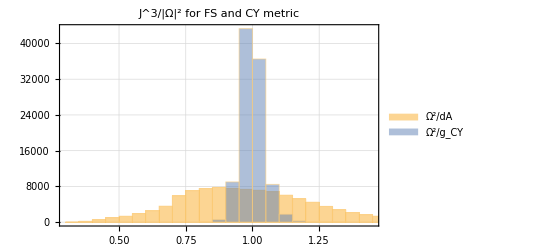

```mathematica
Histogram[{weights/Mean[weights],weightsCY/Mean[weightsCY]},PlotLabel->"J^3/|Ω|^2 for FS and CY metric",PlotTheme->"Detailed",ChartLegends->{ "Ω^2/dA","Ω^2/g_CY"}]
```

To actually access the CY metric, we just call CYMetric on some points

```mathematica
{metrics, session}=CYMetric[{{1,2,3,4,5}},"Model"->NNModel,"Session"->session,"Dir"->outDir];
(*NOTE: The code does not check whether the point is actually on the CY*)
```

```mathematica
{metrics, session}=CYMetric[pts,"Model"->NNModel,"Session"->session,"Dir"->outDir];
```

```mathematica
metrics[[1]]//Chop//MatrixForm
```

(0.18208-2.32831×10^-9 ⅈ | -0.00451971+0.0730248 ⅈ | 0.0381458-0.0506998 ⅈ
-0.00451972-0.0730248 ⅈ | 0.236471-9.77889×10^-9 ⅈ | -0.0709535-0.0478929 ⅈ
0.0381458+0.0506998 ⅈ | -0.0709535+0.0478929 ⅈ | 0.205123-3.84171×10^-9 ⅈ)

And the volume can be computed by integrating det(g). We compare the Kahler classes of the Fubini-Study and the CY metric, and also look at the actual value as computed from ∫J^3

```mathematica
{auxWeights,session}=GetAuxiliaryWeights["all","Dir"->outDir];
{gFSs,session}=FSMetric[pts,"Session"->session,"Dir"->outDir];
{gCYs,session}=CYMetric[pts,"Model"->NNModel,"Session"->session,"Dir"->outDir];
volFS=Round[Mean[Re[auxWeights (Det/@gFSs)]],0.1];
volCY=Round[Mean[Re[auxWeights (Det/@gCYs)]],0.1];
volInt=5;
Print["Kahler moduli:  ",{1}];
Print["Actual volume:  ",volInt];
Print["FS volume:      ",volFS];
Print["CY volume:      ",volCY];
```

Kahler moduli:  {1}

Actual volume:  5

FS volume:      5.

CY volume:      5.

For the Phi Model, we can also get the Kahler potential

```mathematica
{kahler,session}=GetKahlerPotential[pts,"Model"->NNModel,"Session"->session,"Dir"->outDir];
kahler[[;;10]]
```

{0.267758,0.266136,0.342575,0.280808,0.346327,0.296618,0.368267,0.292555,0.320303,0.315405}

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.157287,0.126193,0.113318,0.0886455,0.0779465,0.0732612,0.069813,0.0688366,0.0676161,0.0670007,0.0663871,0.0660586,0.0657323,0.0654625,0.0652556,0.064955,0.0645049,0.0641964,0.0639394,0.0638384,0.063444,0.0631663,0.0626869,0.0623506,0.0619076,0.0614119,0.0607544,0.0599365,0.0585327,0.0569972,0.0552003,0.0535713,0.0516832,0.0499622,0.0479241,0.0455446,0.0432981,0.0411826,0.0395129,0.0381058,0.0371226,0.0360702,0.0354052,0.034609,0.0341559,0.0336295,0.032989,0.0326714,0.0322911,0.0321401},kaehler_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},transition_loss→{0.0087241,0.00364112,0.0050549,0.00671351,0.00585929,0.00483945,0.00392107,0.00313028,0.00261995,0.00227166,0.00203821,0.00187618,0.00174376,0.0016572,0.00158252,0.00152954,0.00149376,0.00147081,0.00144483,0.00142293,0.00141361,0.0014113,0.00142059,0.00144359,0.00145674,0.00148418,0.00154471,0.00163077,0.00176292,0.00191244,0.00207564,0.0021988,0.00228854,0.00236357,0.00248422,0.00260586,0.00270113,0.00271874,0.00272648,0.00273739,0.00273935,0.00272087,0.00271342,0.00271424,0.00270106,0.00267136,0.00266471,0.00266202,0.00263769,0.00264109},volk_loss→{0.00358414,0.0021988,0.00213367,0.00203515,0.00186826,0.00157354,0.00124093,0.00127429,0.00116479,0.0011289,0.00103567,0.00106713,0.000969433,0.000983288,0.00097906,0.000972098,0.000875527,0.00089328,0.000855265,0.000841032,0.000831277,0.000781609,0.000807624,0.000779476,0.000811754,0.00078724,0.000834581,0.000700739,0.000768884,0.000705002,0.000781237,0.000770485,0.000803283,0.00072555,0.000845738,0.000790933,0.000828358,0.000795812,0.000742816,0.000815866,0.000831879,0.000741918,0.000773593,0.00075434,0.000759544,0.000807966,0.000749253,0.000761201,0.000812198,0.000772093},sigma_val→{0.122269,0.118195,0.0992009,0.0857724,0.0832011,0.0810539,0.0768057,0.0766709,0.0742649,0.0745656,0.0749237,0.0739181,0.0738327,0.0725661,0.0751204,0.0728279,0.0737291,0.0742486,0.0711049,0.0726403,0.0713761,0.0719884,0.0713165,0.0714943,0.0708762,0.0711422,0.0688627,0.0662904,0.0655268,0.0636112,0.0601752,0.057839,0.0563796,0.0529946,0.0522716,0.0483077,0.0456805,0.0459426,0.042338,0.0391419,0.0383333,0.037841,0.0374057,0.036206,0.0358671,0.0357787,0.0358866,0.0342788,0.0352674,0.034172},kaehler_val→{5.82499×10^-15,5.8445×10^-15,5.96605×10^-15,6.30187×10^-15,6.36862×10^-15,6.35679×10^-15,6.34639×10^-15,6.30581×10^-15,6.03377×10^-15,5.99461×10^-15,6.00103×10^-15,6.10081×10^-15,6.08047×10^-15,6.02045×10^-15,6.0681×10^-15,5.95298×10^-15,6.12605×10^-15,6.06678×10^-15,6.02886×10^-15,6.08948×10^-15,6.02297×10^-15,6.0891×10^-15,6.0268×10^-15,5.9671×10^-15,6.02825×10^-15,6.02594×10^-15,6.11502×10^-15,6.09461×10^-15,6.14297×10^-15,6.07138×10^-15,6.04742×10^-15,6.16822×10^-15,6.16231×10^-15,6.21423×10^-15,6.22292×10^-15,6.19616×10^-15,6.31658×10^-15,6.21506×10^-15,6.47518×10^-15,6.2651×10^-15,6.30193×10^-15,6.35886×10^-15,6.27647×10^-15,6.25563×10^-15,6.23034×10^-15,6.39999×10^-15,6.2396×10^-15,6.25283×10^-15,6.34125×10^-15,6.31407×10^-15},transition_val→{0.00407262,0.00352976,0.00676902,0.0064467,0.00535435,0.00430118,0.00356975,0.00287577,0.00244152,0.00219198,0.00191742,0.00189351,0.00166108,0.00163891,0.00159887,0.00154481,0.00144623,0.00148015,0.00143776,0.00146202,0.00139738,0.0014879,0.00140868,0.00142136,0.00140549,0.00154396,0.00159805,0.00169707,0.00190714,0.0019721,0.00217934,0.00234013,0.00230161,0.0024225,0.00242967,0.00267486,0.0027799,0.00274285,0.00265257,0.00276355,0.00276701,0.00266116,0.00273155,0.00264228,0.00268943,0.00272081,0.00267525,0.00260582,0.00277375,0.00258642},ricci_val→{0.749761,0.59117,0.498142,0.488905,0.500591,0.483965,0.49265,0.498908,0.475239,0.477545,0.475669,0.492599,0.471202,0.499253,0.483275,0.490064,0.476198,0.486859,0.484558,0.49775,0.482364,0.486247,0.479573,0.476781,0.477849,0.476593,0.471388,0.484954,0.485254,0.453733,0.456531,0.465628,0.456696,0.454473,0.441201,0.450509,0.468784,0.466292,0.460038,0.458587,0.479648,0.465378,0.45778,0.446571,0.473906,0.450767,0.4445,0.444435,0.445203,0.436694},volk_val→{5.02257,4.99982,4.66396,4.7969,4.85053,4.88526,4.84703,4.89348,4.78631,4.83943,4.89377,4.88082,4.84592,4.8647,4.86437,4.90449,4.91585,4.91896,4.82581,4.87712,4.84647,4.91522,4.93472,4.84683,4.89599,4.86623,4.90317,4.85747,4.94855,4.92613,4.89396,4.9565,4.91944,4.97202,4.95329,4.93208,4.96241,4.98112,5.00356,4.93766,4.95518,4.95733,4.95632,4.93699,4.95701,4.97183,4.93549,4.9738,4.94853,4.96005}|>

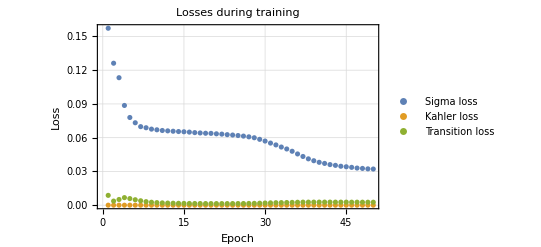

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

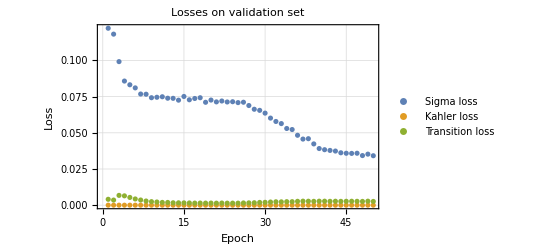

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

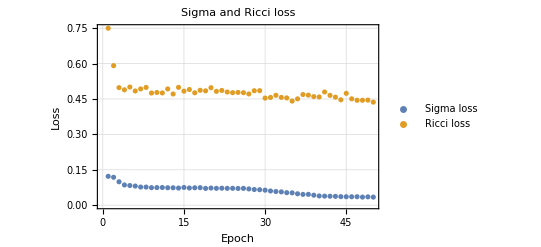

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

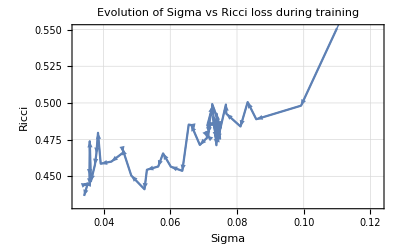

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",AxesLabel->{"Sigma","Ricci"},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Look at eigenvalues of the metric

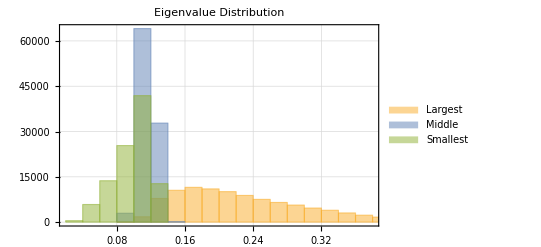

```mathematica
EigVals=Table[Eigenvalues[metrics[[i]]]//Re//Chop,{i,Length[metrics]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```